```mathematica
(*  Checking the existence of the 5-chromatic 372-vertex unit distance graph
embedded in the circumsphere of the icosahedron with unit edge lengths. 
Vsevolod Voronov, Anna Neopryatnaya, Eugene Dergachev 
  e-mail: v-vor@yandex.ru        *)

(*  requires IGraph/M: https://github.com/szhorvat/IGraphM  *)

(*  code from this page 
https://mathandcode.com/2016/06/06/polyhedramathematica.html 
 is used to generate symmetry group *)

(* Numerically check if a square matrix is the identity matrix to within some accuracy *)
isIdentityMatrix[r_]:=(Flatten[N[r-IdentityMatrix[Length[r]]]].Flatten[N[r-IdentityMatrix[Length[r]]]]<0.001);

(* Numerically check if any matrix is the zero matrix to within some accuracy *)
isZeroMatrix[r_]:=(Flatten[N[r]].Flatten[N[r]]<0.001);

(* Numerically test and remove duplicate matrices from a list *)
reduce[list_]:=Union[list,SameTest->(isZeroMatrix[#1-#2]&)];

(* Given a list of square matrices g, this function combines all possible pairs of matrices in all possible orders, and numerically removes all duplicate matrices *)
iterate[g_]:=reduce[FullSimplify[#1.#2]&@@@Tuples[g,2]];

(* Given a generating set of matrices, this function creates a group. If the generators aren't actually a generating set, 
this code runs forever! *)
makeGroup[generators_]:=FixedPoint[iterate,Join[generators,{IdentityMatrix[3]}]];

orbit[point_,group_]:=reduce[#.point&/@group];

(* computing the adjacence matrix of the distance graph *)
(* it's better to check distances numerically before the analytic computation  *)
DistOne[i_,j_]:= (Abs[(Nvertices[[i]]-Nvertices[[j]]).(Nvertices[[i]]-Nvertices[[j]])-1]<0.000001&& FullSimplify[Sum[(vertices[[i]][[k]]-vertices[[j]][[k]])^2,{k,1,3}]]==1);

DistOneN[i_,j_]:= (Abs[(Nvertices[[i]]-Nvertices[[j]]).(Nvertices[[i]]-Nvertices[[j]])-1]<0.000001);

UnitDist[L_]:= Boole[DistOne[#1,#2]&@@@Subsets[L,{2}]];
```

```mathematica
(* icosahedron symmetry group elements *)
(* order = 120 *)
f=(1+Sqrt[5])/2;
icoGenerators={{{-1,0,0},{0,-1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},(1/2 {{1,-f,1/f},{f,1/f,-1},{1/f,1,f}}),{{1,0,0},{0,-1,0},{0,0,1}}};
icoG=makeGroup[icoGenerators];
```

```mathematica
(* 12 icosahedron vertices *)

v= {(Sqrt[5]+1)/4,1/2,0};
icosV=orbit[v,icoG];


(* using 3 points from the embedding of the 9-vertex unit distance graph 
  we compute 3*120 vertices  *)
v11 = 1/4 (1+√(-1+2 √5));
v12 =1/8 (-1-√5+2 √(7/2+(5 √5)/2)) ;
v13 = 1/4 √(5-3 √5+√(2 (7+5 √5)));
v21=Root[1+8 #1+9 #1^2-7 #1^3+28 #1^4+6 #1^5-4 #1^6-#1^7+#1^8&,2]/2;
v22=Root[-1-5 #1+5 #1^2-4 #1^3+9 #1^4-5 #1^5+#1^6-2 #1^7+#1^8&,1]/2;
v23=Root[-1+7 #1-13 #1^2-24 #1^3+4 #1^4+10 #1^5-3 #1^7+#1^8&,2]/2;
v31=Root[1+8 #1+9 #1^2-7 #1^3+28 #1^4+6 #1^5-4 #1^6-#1^7+#1^8&,1]/2;
v32=Root[-1-5 #1+5 #1^2-4 #1^3+9 #1^4-5 #1^5+#1^6-2 #1^7+#1^8&,2]/2;
v33=-Root[-1+7 #1-13 #1^2-24 #1^3+4 #1^4+10 #1^5-3 #1^7+#1^8&,1]/2;

(*  although equations can be solved explicitely, it's more efficient to express the solutions by Root[] objects *)

vect={{v11,v12,v13},{v21,v22,v23},{v31,v32,v33}};
vertices={};
For[i=1,i<=3,i++, vertices=Join[vertices,FullSimplify[orbit[vect[[i]],icoG]]]];

(* here coordinates of all 372 vertices are represented by Root[] objects *)
vertices=Join[vertices,icosV];
Length[vertices]
(* number of vertices *)
```

372

```mathematica
ind=Range[372];

(* numerical form is required to speed up *)
Nvertices=N[vertices, 10];
```

```mathematica
(* pairs of vertices *)
LS = Subsets[ind,{2}];

(* --------------------------------this step consumes most of the time ------------------------------------ *)
(* the numerical-only computation (DistOneN) is much faster, but it doesn't make any sense as a proof -----------*)

AdjMatr = Parallelize[Boole[DistOne[#1,#2]&@@@LS]];

(* ----------------------------- 3-10 min depending of CPU speed -----------------------------------------*)
(* number of edges *)
Total[AdjMatr]
```

1710

```mathematica
ListPointPlot3D[Nvertices]
```

-Graphics3D-

```mathematica
edges={};
For[i=1,i≤Length[LS],i++,If[AdjMatr[[i]]==1,AppendTo[edges,LS[[i]]],]];
Length[edges]
```

1710

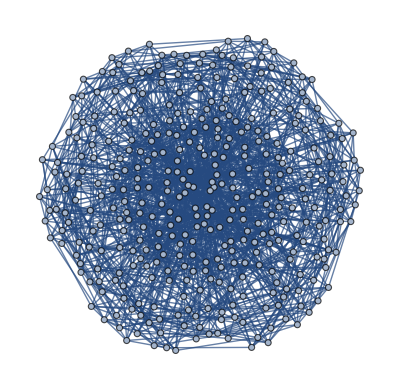

```mathematica
g = Graph[edges]
```

```mathematica
<<IGraphM`
```

IGraph/M 0.3.112 (May 7, 2019)

Evaluate IGDocumentation[] to get started.

```mathematica
IGChromaticNumber[g]
```

5